# (Natural) Splines in Action

Let’s look at some fun examples of using splines!

First, we copy our spline code from last time into a module so we can create splines from data more easily.

```mathematica
Spline[Data_]:=Module[{h,a,L,U,Diag,M,B,c,b,d,Poly,P},
h[n_]:=Data[[n+1]][[1]]-Data[[n]][[1]];
a=Table[Data[[i]][[2]],{i,1,Length[Data]}];
L=DiagonalMatrix[Table[h[i],{i,1,Length[Data]-2}]~Join~{0},-1];
U=DiagonalMatrix[{0}~Join~Table[h[i],{i,2,Length[Data]-1}],1];
Diag=DiagonalMatrix[{1}~Join~Table[2(h[i]+h[i+1]),{i,1,Length[Data]-2}]~Join~{1}];
M=L+U+Diag;
B={0}~Join~Table[(3/h[i+1])(a[[i+2]]-a[[i+1]])-(3/h[i])(a[[i+1]]-a[[i]]),{i,1,Length[Data]-2}]~Join~{0};
c=LinearSolve[M,B];
b=Table[(1/h[i])(a[[i+1]]-a[[i]])-(h[i]/3)(2c[[i]]+c[[i+1]]),{i,1,Length[Data]-1}];
d=Table[(c[[i+1]]-c[[i]])/(3h[i]),{i,1,Length[Data]-1}];
Poly=Table[a[[i]]+b[[i]](x-Data[[i]][[1]])+c[[i]](x-Data[[i]][[1]])^2+d[[i]](x-Data[[i]][[1]])^3,{i,1,Length[Data]-1}];
P=Piecewise[Table[{Poly[[i]],Data[[i]][[1]]≤x≤Data[[i+1]][[1]]},{i,1,Length[Data]-1}]]
]
```

## Example 1

For our first example we will use some of the “curated” data that is accessable from inside Mathematica to analyze population data in France.

### Wolfram Curated Data

Wolfram maintains many databases that can be accessed from within Mathematica. In fact, these are the same databases that Siri accesses when you ask questions about flight data, population data, etc...

An example from the help files is locating the international space station:

```mathematica
With[{data=SatelliteData[LinguisticAssistant,{"Position","SatelliteLocationLine","SatelliteVisibilityDistance"}]},
GeoGraphics[{Gray,Thickness[.005],Arrowheads[{{0.05,0.4},{0.05,0.13}}],Arrow@@data[[2]],Red,PointSize[.01],Point[data[[1]]],Opacity[.1],Black,GeoVisibleRegion[data[[1]]]},GeoCenter->data[[1]],GeoRange->"World"]]
```

-Graphics-

```mathematica
?GeoGraphics
```

GeoGraphics[primitives,options] represents a two-dimensional geographical image.

```mathematica
GeoGraphics[GeoCenter->{36.1367497,-80.27848219999998},GeoZoomLevel->12]
```

-Graphics-

Or maybe we want to plot a geodesic on the Earth from Wake Forest University to Paris, France!

```mathematica
GeoGraphics[]
```

-Graphics-

```mathematica
GeoGraphics[GeoPath[{{36.1367497,-80.27848219999998},{48.8567,2.3508}}],GeoRange->"World",Frame->True]
```

-Graphics-

Speaking of France... we can also access data about countries around the work. For example, we can get the population of France in 2010.

```mathematica
CountryData["France",{"Population",{2010,1,1}}][[1]]
```

### Question: How can we use splines to model population data? In particular, suppose we only have access to population data at 5 year intervals. How can we estimate the population between these data points?

To access the population data we can Table over the Wolfram population database and grab the population at every 5th year.
So that we can check the error in our spline estimate we will also grab the population for each year.

```mathematica
FrancePopData=Table[{year,CountryData["France",{"Population",{year,1,1}}][[1]]},{year,1970,2010,5}]
FullPopData=Table[{year,CountryData["France",{"Population",{year,1,1}}][[1]]},{year,1970,2010,1}];
```

{{1970,5.07632×10^7},{1975,5.26918×10^7},{1980,5.38801×10^7},{1985,5.52815×10^7},{1990,5.67083×10^7},{1995,5.78445×10^7},{2000,5.90478×10^7},{2005,6.09965×10^7},{2010,6.27874×10^7}}

Before we get started we can take a look at the data points.

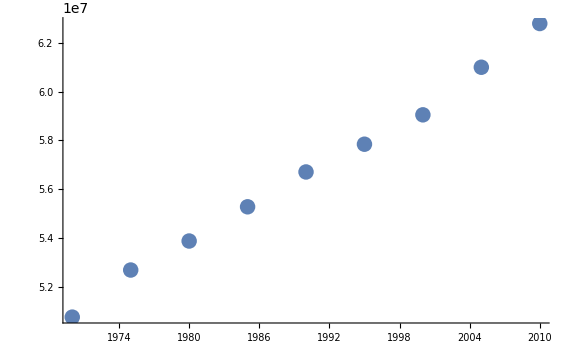

```mathematica
ListPlot[FrancePopData]
```

Since we have a module to generate our spline we can easily compute the polynomials.

```mathematica
FrancePop=Spline[FrancePopData]
```

Piecewise[{{5.07632×10^7+428096. (-1970+x)+2.32831×10^-11 (-1970+x)^2-1694.91 (-1970+x)^3, 1970≤x≤1975}, {5.26918×10^7+300977. (-1975+x)-25423.6 (-1975+x)^2+2552.17 (-1975+x)^3, 1975≤x≤1980}, {5.38801×10^7+238154. (-1980+x)+12858.9 (-1980+x)^2-887.363 (-1980+x)^3, 1980≤x≤1985}, {5.52815×10^7+300191. (-1985+x)-451.502 (-1985+x)^2-502.978 (-1985+x)^3, 1985≤x≤1990}, {5.67083×10^7+257953. (-1990+x)-7996.17 (-1990+x)^2+371.058 (-1990+x)^3, 1990≤x≤1995}, {5.78445×10^7+205820. (-1995+x)-2430.3 (-1995+x)^2+1879.6 (-1995+x)^3, 1995≤x≤2000}, {5.90478×10^7+322487. (-2000+x)+25763.7 (-2000+x)^2-2462.56 (-2000+x)^3, 2000≤x≤2005}, {6.09965×10^7+395433. (-2005+x)-11174.6 (-2005+x)^2+744.976 (-2005+x)^3, 2005≤x≤2010}, {0, True}}]

This isn’t a Pure Function, so if we want to find the population in a particular year we must use a Replacement Rule.

```mathematica
FrancePop[2001]
```

(Piecewise[{{5.07632×10^7+428096. (-1970+x)+2.32831×10^-11 (-1970+x)^2-1694.91 (-1970+x)^3, 1970≤x≤1975}, {5.26918×10^7+300977. (-1975+x)-25423.6 (-1975+x)^2+2552.17 (-1975+x)^3, 1975≤x≤1980}, {5.38801×10^7+238154. (-1980+x)+12858.9 (-1980+x)^2-887.363 (-1980+x)^3, 1980≤x≤1985}, {5.52815×10^7+300191. (-1985+x)-451.502 (-1985+x)^2-502.978 (-1985+x)^3, 1985≤x≤1990}, {5.67083×10^7+257953. (-1990+x)-7996.17 (-1990+x)^2+371.058 (-1990+x)^3, 1990≤x≤1995}, {5.78445×10^7+205820. (-1995+x)-2430.3 (-1995+x)^2+1879.6 (-1995+x)^3, 1995≤x≤2000}, {5.90478×10^7+322487. (-2000+x)+25763.7 (-2000+x)^2-2462.56 (-2000+x)^3, 2000≤x≤2005}, {6.09965×10^7+395433. (-2005+x)-11174.6 (-2005+x)^2+744.976 (-2005+x)^3, 2005≤x≤2010}, {0, True}}])[2001]

```mathematica
FrancePop/.x->2001
```

5.93936×10^7

We can, of course, plot the original data set along with the spline.

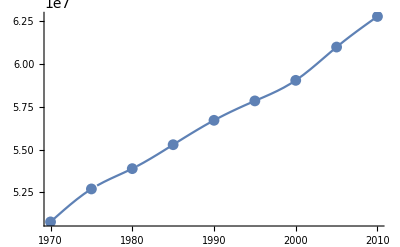

```mathematica
Show[{ListPlot[FrancePopData],Plot[FrancePop,{x,1970,2010}]}]
```

Remember that we actually have access to the yearly population data, so we can see how good our spline approximation is!

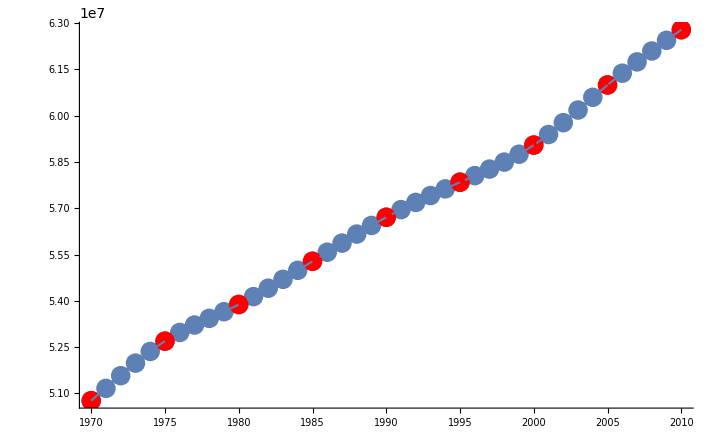

```mathematica
Show[{ListPlot[FullPopData],ListPlot[FrancePopData,PlotStyle->{Large,Red}],Plot[FrancePop,{x,1970,2010}]}]
```

This is kind of astonishing! The fit is incredibly good! To see the error quantitatively we can define a function that returns the actual population in a given year...

```mathematica
ActualPop[d_]:=CountryData["France",{"Population",{d,1,1}}][[1]]
```

```mathematica
ActualPop[2001]
```

5.93907×10^7

... and use it to compute the relative error.

```mathematica
RelError[d_]:=Abs[(FrancePop/.x->d)-ActualPop[d]]/ActualPop[d];
```

So, what is the relative error for our estimation of the population in 2001?

```mathematica
RelError[2001]
```

0.0000482168

```mathematica
AbsoluteError[d_]:=Abs[(FrancePop/.x->d)-ActualPop[d]];
```

```mathematica
AbsoluteError[2001]
```

2863.63

The answer: really small!

Let’s plot the relative error over the entire interval (1970-2010).

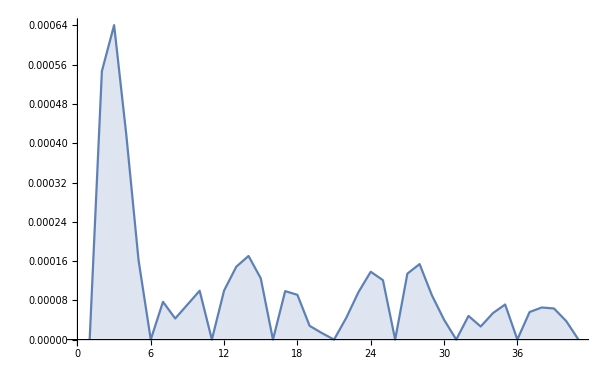

```mathematica
ListLinePlot[Table[RelError[d],{d,1970,2010,1}],{Filling->Axis,PlotRange->All}]
```

There is a spike near 1970... why might this be?

## Example 2

Now for an example from statistics. First we should talk a bit about random processes and probability (crash course on the board!).

### Question: If we roll 10 dice, what is the expected sum of the rolls? How can we compute the probability that the sum will be in a certain interval?

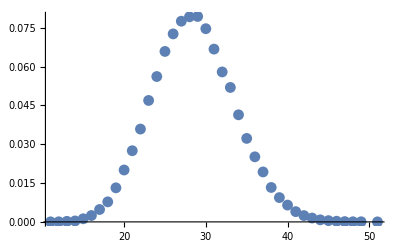

```mathematica
numRolls=10; (*Set the number of dice we will roll in each trial*)
numSamples=100000; (*Set the number of trials we will take*)
(*To summarize: we will roll 10 dice 100,000 times*)
box={1,1,1,2,2,2,2,3,4,4,4,5,6}; (*The dice are weighted and this list gives the possible outcomes*)
Roll[n_]:=RandomChoice[box,{n}]; (*Roll[n_] will roll n_ dice*)
Rolls=Table[Roll[numRolls],{i,1,numSamples}]; (*Rolls will perform numSamples trials (which is to roll numRolls dice*)
RollData=Table[Total[Rolls[[i]]],{i,1,numSamples}];(*RollData computes the sum of each trial*)
Data=Tally[RollData]; (*To create our distribution we need to count how many times we got each outcome*)
NormData=Table[{Data[[i,1]],Data[[i,2]]/numSamples},{i,1,Length[Data]}];(*We normalize the data by dividing each sum by numSamples (so that the total area under the curve is 1)*)
ListPlot[NormData]
```

Now we are ready to compute the spline!

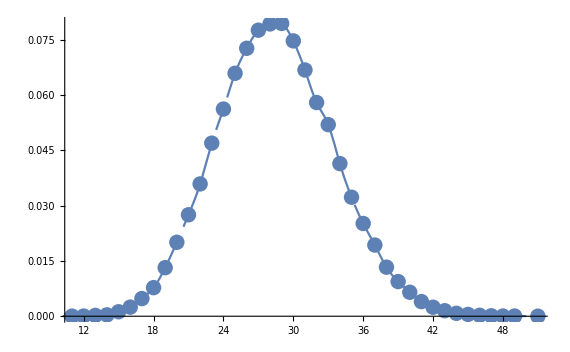

```mathematica
SDist=Spline[Sort[NormData]];
Show[{ListPlot[NormData],Plot[SDist,{x,5,50}]}]
```

To answer our first question we can simply find the maximum value of our spline! We could use calculus, but we have Mathematica!

```mathematica
N[Maximize[SDist,x]]
```

{0.0797747,{x→28.6224}}

To answer our second question we can simply integrate our spline over whatever interval we wish.

```mathematica
N[Integrate[SDist,{x,28,29}]]
```

0.0796161

## Example 3

Our third example is geometric! A random walk is a path in $\mathbb{R}^3$ that is generated by a random process. We will look at random lattice walks which are walks where each steps is to an integer point.

```mathematica
numSteps=1000; (*Set the number of steps in each walk*)
Steps={{1,0,0},{0,1,0},{0,0,1},{-1,0,0},{0,-1,0},{0,0,-1}}; (*At each step we go 1 unit in a coordinate direction*)
ChooseStep:=RandomChoice[Steps,{1}]; (*ChooseStep will randomly choose a direction*)
Step[Start_]:=Start+ChooseStep[[1]]; (*Step implements taking a single step. Note that ChooseStep returns a list, so it must be derefenced*)
RandomWalk[Start_]:=NestList[Step,Start,numSteps]; (*To generate the walk we can use NestList*)
W=RandomWalk[{0,0,0}];
Graphics3D[{Line[W]},BoxRatios->Automatic]
```

-Graphics3D-

Let’s take a look at several random walks.

```mathematica
Colors={Red,Blue,Green,Orange,Yellow,Black};
Show[Table[Graphics3D[{Colors[[i]],Line[RandomWalk[{0,0,0}]]}],{i,1,6}]]
```

-Graphics3D-

After each walk you end up some distance from the origin... which begs the question:

### Question: If you take a random lattice walk of length 1000, how far from the origin do you expect to end up? What is the probality that your distance from the origin will be in some interval?

The setup here is basically the same as the last example. We will take a large number of random walks and then build the distribution as a spline on that data set. Because this code can take a while to run we will start by looking at random walks of length 100.

```mathematica
numSteps=100;(*Set the number of steps for each walk*)
numSamples=1000; (*Set the total number of walks to take*)
Steps={{1,0,0},{0,1,0},{0,0,1},{-1,0,0},{0,-1,0},{0,0,-1}}; (*At each step we go 1 unit in a coordinate direction*)
ChooseStep:=RandomChoice[Steps,{1}];  (*ChooseStep will randomly choose a direction*)
Step[Start_]:=Start+ChooseStep[[1]];  (*Step implements taking a single step. Note that ChooseStep returns a list, so it must be derefenced*)
TakeWalk[Start_]:=Nest[Step,Start,numSteps]; (*TakeWalk will generate the walk, but this time we use Nest (instead of NestList) because we only really care about where the walk ends*)
```

Let’s test out TakeWalk.

```mathematica
TakeWalk[{0,0,0}]
```

{-3,12,3}

To take our walks we start with a list of size numSamples with each element equal to the origin.

```mathematica
Starts=Table[{0,0,0},{i,1,numSamples}];
```

To actually take the walks we can Map TakeWalk over the list Starts. AbsoluteTiming will tell us how long (by the wall clock) the computation took.

```mathematica
TimedWalks=AbsoluteTiming[Map[TakeWalk,Starts]];
TimedWalks[[1]]
```

0.48605

This is a perfect time us parallel processing since the walks are completely independent. Let’s play around a bit to see how much faster the parallelized version is.

```mathematica
TimedWalksParallel=AbsoluteTiming[ParallelMap[TakeWalk,Starts]];
TimedWalksParallel[[1]]
```

0.5

Since AbsoluteTiming returns a pair (time, data) we need to grab the data to analyze the walks.

```mathematica
Walks=TimedWalksParallel[[2]];
```

We can take a look at the cloud of endpoints (the aspect ratio is not cooperating).

```mathematica
ListPointPlot3D[Walks,AspectRatio->1]
```

-Graphics3D-

Where is the center of the cloud of endpoints for the walks?

```mathematica
N[Mean[Walks]]
```

{0.058,-0.175,0.275}

In theory, what should this be?

To compute the distances we can ParallelMap the Mathematica function Norm over the list of Walks.

```mathematica
Dists=ParallelMap[Norm,Walks];
```

We will now tally up the data to generate the histogram. The data will be fairly noisy and one way to smooth things out it to take larger sizes for the class intervals. Deciding how to choose the size of the class intervals can be tricky business... but that is the topic for a course in sampling!

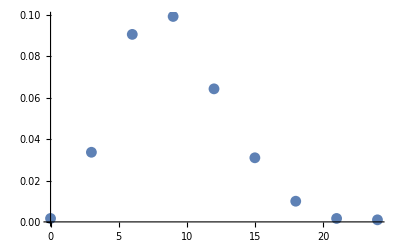

```mathematica
classSize=3;
Data=Tally[Round[Dists,classSize]]; (*To create our distribution we need to count how many distances fall into our class intervals*)
NormData=Sort[Table[{Data[[i,1]],Data[[i,2]]/(Length[Dists]*classSize)},{i,1,Length[Data]}]];
(*We normalize the data by dividing each by the product of numSamples and the size of each class interval (so that the total area under the curve is 1)*)
Show[{ListPlot[Sort[NormData]]}]
```

Out handy Spline module will happily compute the splines.

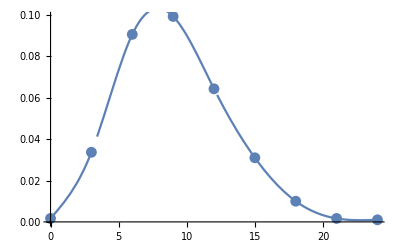

```mathematica
WalkP=Spline[NormData];
Show[{ListPlot[Sort[NormData]],Plot[WalkP,{x,First[NormData][[1]],Last[NormData][[1]]}]}]
```

We can find the most likely distance by maximizing over the spline.

```mathematica
N[Maximize[WalkP,x]]
```

{0.103232,{x→7.8803}}

It is interesting to compare this to the average distance.

```mathematica
N[Mean[Dists]]
```

9.12413

This is evidence that the distances are not normally distributed!

The total integral should be 1.

```mathematica
N[Integrate[WalkP,{x,First[NormData][[1]],Last[NormData][[1]]}]]
```

As we should expect, the integral isn’t exactly one.

To compute probabilities that the distance will be in some interval we can integrate the spline.

```mathematica
N[Integrate[WalkP,{x,15,20}]]
```

### A Larger Dataset

I ran this code at home taking 1,000,000 samples of walks with step size 1000. It took almost 4 hours running on 4 i7 cores. I saved the data to file (the file is ~14 MB) so that we can import it and analyze it.

```mathematica
SetDirectory[NotebookDirectory[]];
LargeSample=Import["walks.dat"];
```

Again, we compute the distance from the origin from each of the walks (and take a look at the timing).

```mathematica
DistsTiming=AbsoluteTiming[ParallelMap[Norm,LargeSample]];
```

```mathematica
DistsTiming[[1]]
```

27.79778

```mathematica
Dists=DistsTiming[[2]];
```

To avoid doing this computation again we can export this data to file. Import and Export work well when importing and exporting lists. If you export a list you can just import it and it will come back in as a list.

```mathematica
Export["dists.dat",Dists];
```

Now, we can look at the histogram for all this data!

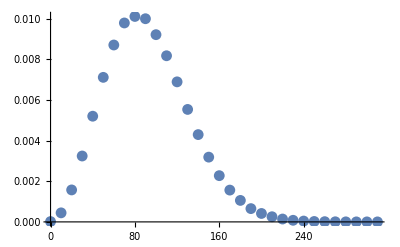

```mathematica
classSize=10;
Data=Tally[Round[Dists,classSize]]; (*To create our distribution we need to count how many distances fall into our class intervals*)
NormData=Sort[Table[{Data[[i,1]],Data[[i,2]]/(Length[Dists]*classSize)},{i,1,Length[Data]}]];
(*We normalize the data by dividing each by the product of numSamples and the size of each class interval (so that the total area under the curve is 1)*)
Show[{ListPlot[Sort[NormData]]}]
```

Computing the splines is the same as before.

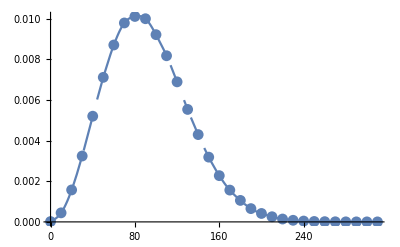

```mathematica
WalkP=N[Spline[NormData]];
Show[{ListPlot[Sort[NormData]],Plot[WalkP,{x,First[NormData][[1]],Last[NormData][[1]]}]}]
```

```mathematica
N[Maximize[WalkP,x]]
```

{0.0101279,{x→83.4142}}

```mathematica
N[Mean[Dists]]
```

92.0813

```mathematica
N[Integrate[WalkP,{x,First[NormData][[1]],Last[NormData][[1]]}]]
```

```mathematica
N[Integrate[WalkP,{x,150,200}]]
```